# ELE 489: Discrete Fourier Transform

## Heath Buchanan / Taylor Brookes

## Due Date:

## Introduction

For this lab we will gain experience implementing Discrete Fourier Transforms(DFT) and Inverse Discrete Fourier Transforms (IDFT). The DFT is a well known finite-length transform with use in digital signal processing. It is used to perform Fourier analysis of finite-duration sequences. The Fast Fourier Transform (FFT) allows computers to efficiently calculate the different frequency components in time-varying signals and reconstruct them from a set of frequency components.

## Problem 1

The N-point discrete Fourier transform (DFT) of a finite-length real or complex sequence x[n] of length N is defined:

X[k] = ∑_(n=0)^(N-1) x[n] ⅇ^(- j (2π)/N k n),			k=0,1,...,N-1

The inverse discrete Fourier transform (IDFT) is given by

x[n] =1/N ∑_(k=0)^(N-1) X[k]  ⅇ^(j (2π)/N k n),		n=0,1,...,N-1

Write the code for the forward and inverse DFT transforms. Name the functions dft and idft, respectively. Each function should take one argument. For example, the input to the dft function should be list of samples of a sequence. The function should return a list of the same length containing the Fourier coefficients.
a) write the code using nested Do and For loops
b) write functions that will result in shorter execution times. Use RepeatedTiming[dft[x];] to show how long it takes.

The first step was to establish some lists to use with our dft function.

```mathematica
x={1,1/ⅈ,0,-1/ⅈ};
```

```mathematica
xi={1,-1,1,3};
```

```mathematica
x2={90,50,40,30,80,70};
```

```mathematica
x2i = {360.,60.+51.96152422706631 ⅈ,0.-17.32050807568877 ⅈ,60.,0.+17.32050807568877 ⅈ,60.-51.96152422706631 ⅈ};
```

These lists were simply pulled from some of the DFT lecture notes and examples used. “x” + “x2” have their respective inverses “xi” and “x2i”. This is used to check the accuracy of our DFTs and IDFTs.

To develop the DFT, we called our method “dft” as per instructions and established an argument (discrete sequence) to be used called “x”. This method passes a list generated by the user called “x” and outputs the DFT.

Next, we established variables to be used in the loop. These were taken directly from the defining DFT summation above:

lenX = the length of the sequence, namely the argument from the user who calls the function we are creating.
y =  the output of the sequence; this is what is continuously updated and returned after the function is completed.
k = the sequence index of the output DFT; this index iterates at 1/4^th the speed of the next variable for lenX = 4.
n = the sequence index of the input signal; this variable goes from 0 to lenX - 1.

Our first DFT function was formulated simply by using nested For loops, as is done with most beginner programming. “lenX” is initially defined as the length of the input sequence, and done so to make the code more readable. Next, a table of zeros is initialized equal to the size of the length of the argument. Then, since the k variable indexes only after all of the n variables have first been run through, we establish “k” in the outer For loop. Inside the nested For loop, we now set the indexing for the “n” variable to start at 0 and index until n iterates to the value of lenX. Following, we enter the summation formula directly from above. However, since the Wolfram language doesn’t index a list starting at 0, but 1, we have to tell our function to start at 1 using” k+“1 and” n+1”. Finally, we output the generated list “y” to the user.

```mathematica
dft[x_] := Module[{k,n,y,lenX},
lenX = Length[x];
y  = Table[0, {lenX}];
For[k=0,k<lenX,k++,
For[n=0,n<lenX,n++,
y[[k+1]] += x[[n+1]]*ⅇ^((-ⅈ)(π*2/lenX)(k)(n))
]
]
;y//N
]
```

The next DFT is the same formula implemented with a Do loop. The Do loop iterates the second list variable first, so the indexing for “k” is listed first and the “n” variable second.

```mathematica
dft2[x_] := Module[{k,n,y,lenX},
lenX = Length[x];
y = Table[0,{lenX}];
k = 0;
n = 0;
Do[y[[k+1]] += x[[n+1]]*ⅇ^((-ⅈ)(π*2/lenX)(k)(n)),{k,0,lenX-1},{n,0,lenX-1}]
;y//N
]
```

Our third DFT function is taken directly from the DFT notebook example in order to compare in RepeatedTiming.

```mathematica
dft3[x_]:=(L=Length[x];
Table[Sum[x[[n+1]]*
ⅇ^((-ⅈ)(π*2/L)(k)(n)),
{n,0,L-1}],
{k,0,L-1}
]
)
```

These are the results of each of our functions using the list “x” defined above:

Using nested For loops

```mathematica
dft[x]
```

{1.,-1.,1.,3.}

Using a Do loop

```mathematica
dft2[x]
```

{1.,-1.,1.,3.}

Using the Jankowski’s DFT Notebook

```mathematica
dft3[x]//N
```

{1.,-1.,1.,3.}

Our next result is found using the built-in Wolfram language Fourier to compare our results with.

```mathematica
Fourier[x,FourierParameters->{1,-1}]//Chop
```

{1.,-1.,1.,3.}

These are the results of each of our functions using the “x2” list defined above:

Using nested For loops

```mathematica
dft[x2]//Chop
```

{360.,60.+51.9615 ⅈ,0.-17.3205 ⅈ,60.,0.+17.3205 ⅈ,60.-51.9615 ⅈ}

Using a Do loop

```mathematica
dft2[x2]//Chop
```

{360.,60.+51.9615 ⅈ,0.-17.3205 ⅈ,60.,0.+17.3205 ⅈ,60.-51.9615 ⅈ}

Finally, comparing them to the built-in Fourier function

```mathematica
Fourier[x2,FourierParameters->{1,-1}]//Chop
```

{360.,60.+51.9615 ⅈ,0.-17.3205 ⅈ,60.,0.+17.3205 ⅈ,60.-51.9615 ⅈ}

Here is a RepeatedTiming comparison of the speeds of each of our developed functions with Jankowski’s example and the built-in Fourier function:

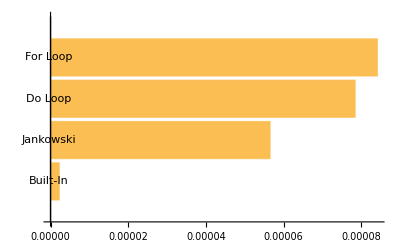

```mathematica
BarChart[{RepeatedTiming[Fourier[x,FourierParameters->{1,-1}];][[1]],RepeatedTiming[dft3[x];][[1]],RepeatedTiming[dft2[x];][[1]],RepeatedTiming[dft[x];][[1]]},BarOrigin->Left,ChartLabels->{"Built-In","Jankowski","Do Loop","For Loop"}]
```

The next task in Problem 1 was to develop the Inverse Discrete Fourier Transform. We used the same variables from the DTF function above.

The first function is made with nested For loops. Using the same method from above, we refer to the input argument to obtain the proper length of our “y” table initialization. We then specify the two indexing variables, but because the IDFT takes the DFT as an input “k” instead of being the output of the DFT, “k” is indexed only after the output signal “n” is indexed with For loops. Do loops executes indexing in the opposite order.

These are the variables:

lenX = the length of the sequence; namely the length of the user’s input argument same as for the DFT
y = the output sequence returned by the function after operating
k = the sequence index of the input DFT
n = the sequence index of the output signal

Our initial IDFT using nested For loops is as follows:

```mathematica
idft[x_] := Module[{k,n,y,lenX},
lenX = Length[x];
y  = Table[0, {lenX}];
For[n=0,n<lenX,n++,
For[k=0,k<lenX,k++,
y[[n+1]] += x[[k+1]]*ⅇ^((ⅈ)(π*2/lenX)(k)(n))
];y[[n+1]]*= (1/lenX)
];y//N
]
```

The second example is the IDFT function as a nested Do loop, used to show in RepeatedTiming that Do loops are marginally faster than For loops.

```mathematica
idft2[x_] := Module[{k,n,y,lenX},
lenX = Length[x];
y = Table[0,{lenX}];
Do[Do[y[[n+1]] += x[[k+1]]*ⅇ^((ⅈ)(π*2/lenX)(k)(n)),{k,0,lenX-1}];y[[n+1]]*= (1/lenX),{n,0,lenX-1}]
;y//N
]
```

These are the IDFT functions using the list “xi” first with the nested For loop example

```mathematica
idft[xi]
```

{1.,0.-1. ⅈ,0.,0.+1. ⅈ}

Next with the Do loop

```mathematica
idft2[xi]
```

{1.,0.-1. ⅈ,0.,0.+1. ⅈ}

Finally, using the built-in InverseFourier function

```mathematica
InverseFourier[xi,FourierParameters->{1, -1}]//Chop
```

{1.,0.-1. ⅈ,0,0.+1. ⅈ}

We run more examples using the list “x2i” first the the For loop function

```mathematica
idft[x2i]//Chop
```

{90.,50.,40.,30.,80.,70.}

With the Do loop function

```mathematica
idft2[x2i]//Chop
```

{90.,50.,40.,30.,80.,70.}

And lastly with the built in InverseFourier function

```mathematica
InverseFourier[x2i,FourierParameters->{1, -1}]//Chop
```

{90.,50.,40.,30.,80.,70.}

Here we chart the RepeatedTiming results comparing the For, Do, and built-in functions

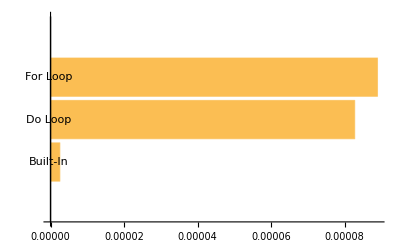

```mathematica
BarChart[{RepeatedTiming[InverseFourier[xi,FourierParameters->{1,-1}];][[1]],RepeatedTiming[idft2[xi];][[1]],RepeatedTiming[idft[xi];][[1]]},BarOrigin->Left,ChartLabels->{"Built-In","Do Loop","For Loop"}]
```

This shows that Do loops and For loops take approximately the same amount of time, with Do loops being only slightly faster. Each time we evaluate RepeatedTiming, we get a slightly different answer, as RepeatedTiming is an average of a number of executions and each execution takes a marginally varying amount of time due to things such as memory storage.

## Problem 2

Obtain the DFTs of the following sequences:

(a). Random sequence, uniformly distributed:

```mathematica
xa=RandomReal[{-1,1},128];
ListPlot[{Labeled[xa,"Input (xa)"],Labeled[Abs[dft[xa]],"DFT (xa)"]},Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full]
```

-Graphics-

We were given a list of 128 random real numbers between -1 and 1. We ran these through our developed DFT above in the ListPlot.

What does the magnitude of the DFT of a random signal look like? Describe.

The magnitude of the DFT of a random signal looks like a lot of noise. The magnitude of both sequences is shown below, with all values being positive as a result of the magnitude function. The graph has odd symmetry around the middle (65), excluding the [[1]] on the opposite side, which would be [[129]]. Taking the mean, we see that Mean[xa] is close to 0, while Mean[Abs[xa]] is close to 0.5 as we expect. We see that Mean[dft[xa]] is close to 0 as well, while Mean[Abs[dft[xa]]] is close to 5. Not quite sure why this is the case, but it is. Overlaying the graphs doesn’t seem to help make sense of all the random noise.

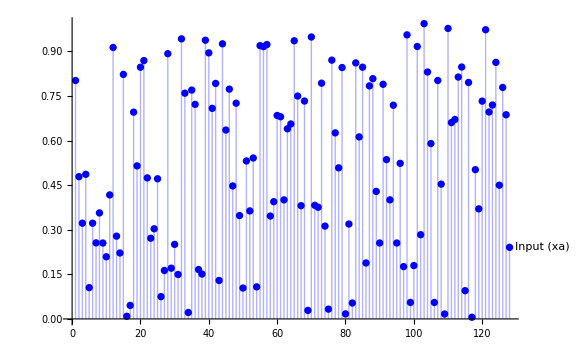
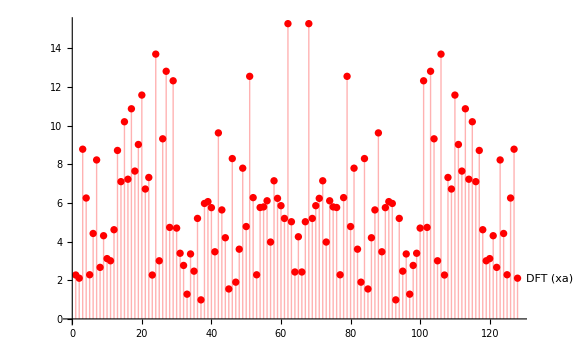

```mathematica
Overlay[{ListPlot[Labeled[Abs[xa],"Input (xa)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Large,PlotStyle->Blue],ListPlot[Labeled[Abs[dft[xa]],"DFT (xa)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Large,PlotStyle->Red]}]
```

(b). Gaussian shaped sequence with noise:

```mathematica
xb=GaussianMatrix[{{64},{6}}]/Max[GaussianMatrix[{{64},{6}}]]+RandomReal[{-0.05,0.05},129];
ListPlot[{Labeled[xb,"Input (xb)"],Labeled[Abs[dft[xb]],"DFT (xb)"]},Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full]
```

-Graphics-

Above is the plot of a given sequence “xb” constructed with a GaussianMatrix + 129 random real numbers between -.05 and .05. This distribution is graphed to the left while our DFT of the result is graphed to the right, with the plot range being that of the DFT to show the u-shaped distribution of the DFT in its full range, rather than being cut off by the range of the Gaussian matrix. Below is graphed the Gaussian matrix using a range of its max value (1) and the resulting DFT with a range of it’s max value (~15).

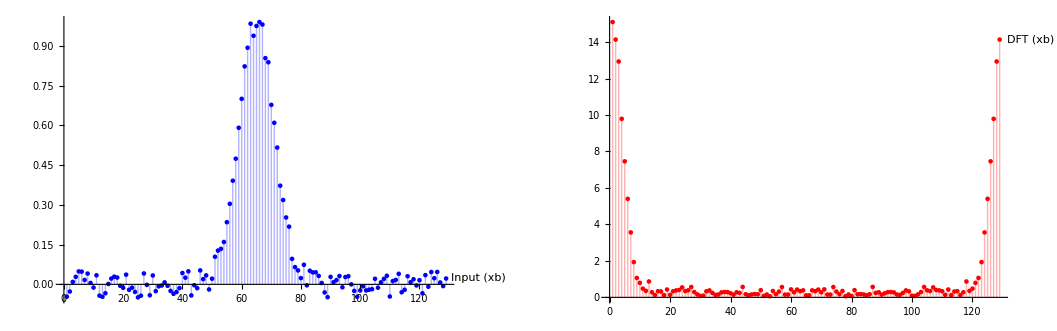

```mathematica
GraphicsRow[{ListPlot[Labeled[xb,"Input (xb)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Blue],ListPlot[Labeled[Abs[dft[xb]],"DFT (xb)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Red]}]
```

What does the magnitude of the DFT of the Gaussian sequence look like? Describe.

The magnitude of the DFT of the random Gaussian sequence is U-shaped. For the Gaussian signal, the frequency domain representation has most of the energy concentrated around the center frequency, in our case 64, which corresponds to the peak of the Gaussian function in the time domain. Moving towards the tails, the energy decreases, giving us the U shape we see in the DFT.

(c) Multi-tone sinusoidal sequence:

```mathematica
k=RandomInteger[{6,36},3];
xc=Table[Sin[(2.π)/135 k⟦1⟧ n]+3/2 Sin[(2.π)/150 k⟦2⟧ n]+2/3 Cos[(2.π)/155 k⟦3⟧ n],{n,0,127}];
ListPlot[{Labeled[xc,"Input (xc)"],Labeled[Abs[dft[xc]],"DFT (xc)"]},Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full]
```

-Graphics-

Lastly for Problem 2, we have a multi-tonal sequence. The above ListPlot poses the input “xc” next to its DFT using our function. The below ListPlot graphs the functions with their respective ranges.

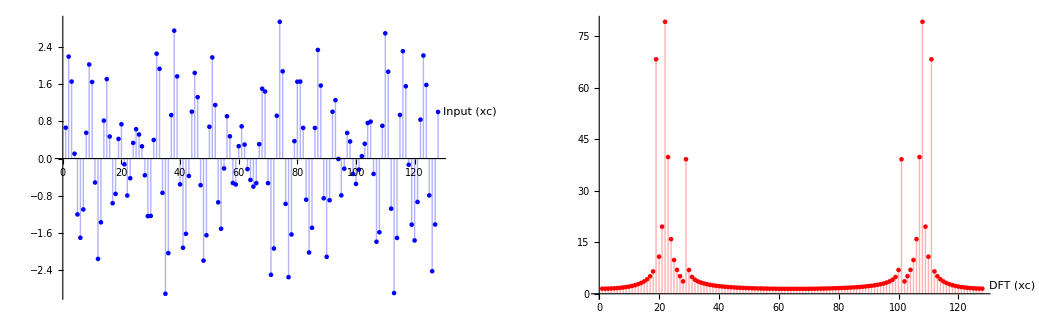

```mathematica
GraphicsRow[{ListPlot[Labeled[xc,"Input (xc)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Blue],ListPlot[Labeled[Abs[dft[xc]],"DFT (xc)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Red]}]
```

The magnitude of the DFT of the multi-tonal sequence is 3 u-shapes superimposed upon the same graph. This is like the Gaussian function above, but of 2 different sine functions  and 1 cosine function with different peaks of energy, so there are 6 total peaks, symmetric about their centers. We should see 6 different peaks, 4 for our 2 sine functions and 2 for the cosine function. The lower the frequency, the farther apart the peaks in its DFT become.

What does the magnitude of the DFT of the multi-tone sequence look like? Describe. How many DFT peaks do you see? How many should you see? 

The magnitude of the DFT looks similar to the gaussian, but with peaks spread out over the graph instead of at the ends. Symmetrical graph. There are 6 DFT peaks. There are 3 sinusoidal functions, which means that there should be 6 peaks, which there are.

Taylor added an additional test with the image from Problem 3 and we ran the same tests.

(d)Image pixels:

```mathematica
xd=PixelValue[-Graphics-,{RandomInteger[{15,89}],All}];
ListPlot[{Labeled[xd,"Input (xd)"],Labeled[Abs[dft[xd]],"DFT (xd)"]},Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full]
```

-Graphics-

Above is the input signal from the image next to the DFT of it. Below we have the DFT scaled  to the input still showing symmetry about the midpoint with peaks reaching above the graph on the ends.

```mathematica
ListPlot[{Labeled[xd,"Input (xd)"],Labeled[Abs[dft[xd]],"DFT (xd)"]},Filling->0,PlotRange->1,PlotLayout->"Row",ImageSize->Full]
```

-Graphics-

## Problem 3

Obtain the IDFTs of the following three complex sequences:

```mathematica
Xa=;
```

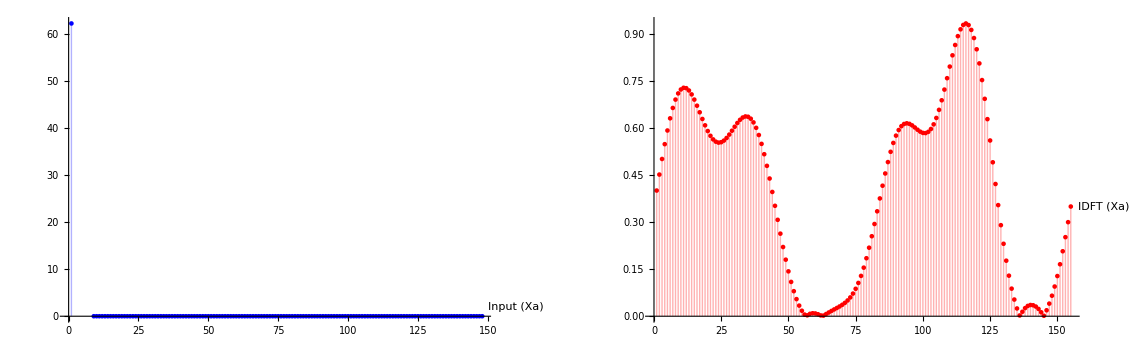

```mathematica
GraphicsRow[{ListPlot[Labeled[Xa,"Input (Xa)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Blue],ListPlot[Labeled[Abs[idft[Xa]],"IDFT (Xa)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Red]}]
```

There’s a bunch of 0’s in the middle of the graph, with random numbers on each end of the parent signal/sequence DFT ranging from ~60 to ~-20, which is symmetrical. The IDFT magnitude graph is not symmetrical. We couldn’t figure out how to graph the negative values in the “Xa” sequence.

```mathematica
Xb=;
```

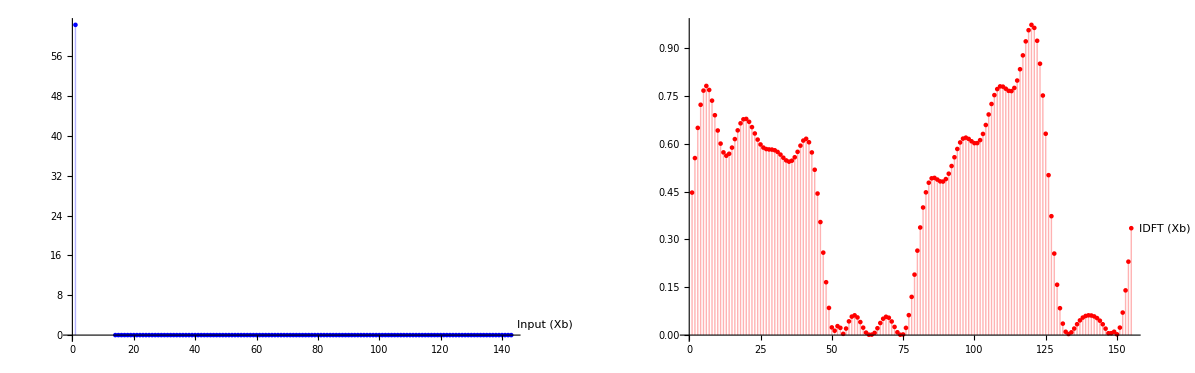

```mathematica
GraphicsRow[{ListPlot[Labeled[Xb,"Input (Xb)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Blue],ListPlot[Labeled[Abs[idft[Xb]],"IDFT (Xb)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Red]}]
```

Again, there’s a bunch of 0’s in the middle of the graph, but this time less of them. There are random numbers on each end of the parent signal/sequence DFT, which is symmetrical. The IDFT magnitude graph is not symmetrical and looks similar to the previous one, except with more wavy and less smooth.

```mathematica
Xc=;
```

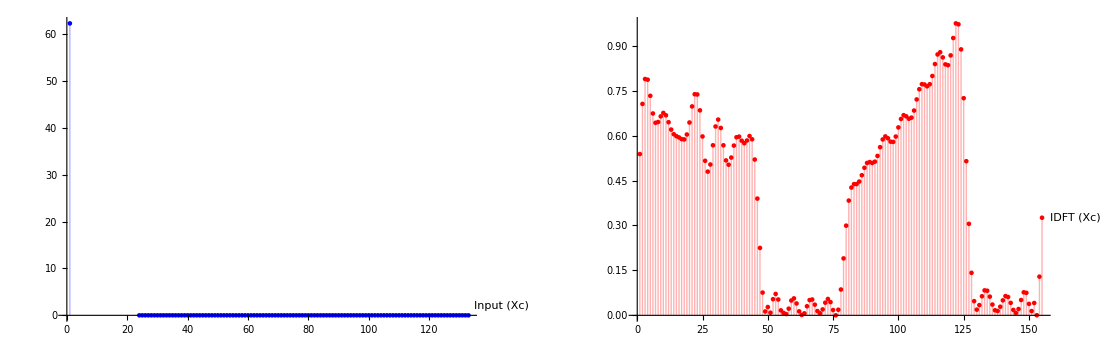

```mathematica
GraphicsRow[{ListPlot[Labeled[Xc,"Input (Xc)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Blue],ListPlot[Labeled[Abs[idft[Xc]],"IDFT (Xc)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Medium,PlotStyle->Red]}]
```

The DFT is a sampling of the DTFT, which is a continuous function. By comparing IDFT graphs from A to B and C, we notice that the original function must be less averaged/smooth for each of them, with the most smooth signal coming from A.

Compare the IDFTs with the sequence created below and comment on the results.

```mathematica
xd=PixelValue[-Graphics-,{80,All}];
```

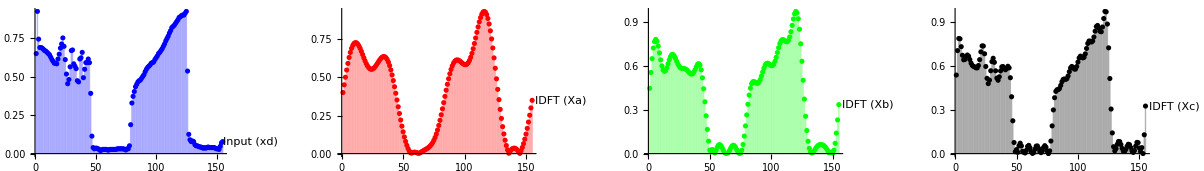

```mathematica
GraphicsRow[{ListPlot[Labeled[xd,"Input (xd)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full,PlotStyle->Blue],ListPlot[Labeled[Abs[idft[Xa]],"IDFT (Xa)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full,PlotStyle->Red],
ListPlot[Labeled[Abs[idft[Xb]],"IDFT (Xb)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full,PlotStyle->Green],
ListPlot[Labeled[Abs[idft[Xc]],"IDFT (Xc)"],Filling->0,PlotRange->All,PlotLayout->"Row",ImageSize->Full,PlotStyle->Black]}]
```

In comparing the input “xd” with Xa, Xb, and Xc, we notice that Xa has the most zeros making the approximation the least accurate and the file-size smaller because there is less data. Xa is the least approximate and Xc is the most approximate in reference to the original data. Xc retains the most amount of values from xd instead of filling the list with zeros as with Xa. As seen in Xc, we try to approximate the original input “xd” by using consecutive sinusoidal functions via the IDFT.

## Problem 4

Measure and plot the execution time of your DFT code for N=2^n with n=4,5,...,12. How does the execution time change as the length of the signal is doubled?

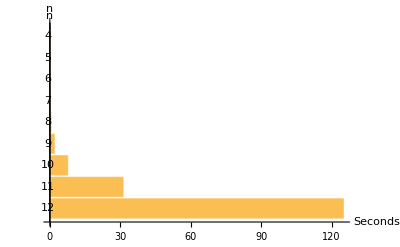

```mathematica
BarChart[{RepeatedTiming[dft[RandomComplex[1+ⅈ,2^12]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^11]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^10]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^9]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^8]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^7]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^6]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^5]];][[1]],RepeatedTiming[dft[RandomComplex[1+ⅈ,2^4]];][[1]]},BarOrigin->Left,ChartLabels->{"12","11","10","9","8","7","6","5","4"},AxesLabel-> {"n","Seconds"}]
```

The execution time increases 4-fold when the length of the signal is doubled.

## Conclusion

The discrete Fourier transform (DFT) and inverse discrete Fourier transform (IDFT) are used for signal processing and analysis. The DFT provides a way to represent a discrete finite sequence of data as a sum of sinusoidal components, while the IDFT allows us to reconstruct the original signal. We used nested For loops and Do loops to show that they can both be used to calculate the DFT and IDFT, and compared their timing to show that Do loops are slightly faster, but neither are anywhere near the speed of the built-in Fourier transform methods in Mathematica. We saw how the DFT outputs a symmetrical graph with peaks due to sinusoidal inputs, that a Gaussian matrix outputs a u-shaped DFT due to the largest values being at the center of each peak and the DFT only takes half of its value, and that the DFT of an image column produces approximately the same as a gaussian matrix. We learned that the DFT only requires half of its data to be used for processing, since it is symmetrical. We learned that adding zeroes in the middle of a DFT decreases the size that the file takes up, allowing for further compression, at the loss of data; however, the approximation of the original signal is output as a smoothed sequence due to averaging. Finally, we showed that increasing the length of the sequence “N” by 2^n, it takes us 4 times as long to execute our DFT.